## Topic

### Definition / Theorem

This is text.

#### Example

## Gamma Function

```mathematica
ClearAll[gamma]
(*gamma[s_]:=Integrate[x^(s-1)ⅇ^-x,{x,0,Infinity}]*)
gamma[x_]:=Integrate[t^(x-1)ⅇ^-t,{t,0,Infinity}]
gamma2[x_]:=1/x Integrate[t^x ⅇ^-t,{t,0,Infinity}]
gamma[t]//TraditionalForm
Log[10.,Gamma[70]]
```

Integrate::idiv: Integral of ⅇ^-t t^(-1+t) does not converge on {0,∞}.

∫_0^∞ ⅇ^-t t^(t-1)ⅆt

98.2333

2.54926

2.54926

120

2.54926

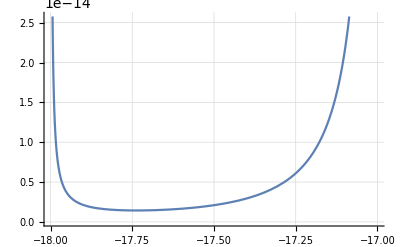

```mathematica
gamma[3.25]//N
gamma2[3.25]//N
gamma[6]
Gamma[3.25]//N
Plot[Gamma[x],{x,-18,-17},GridLines->Automatic]
```

```mathematica
gamma[z_]:=Integrate[t^(z-1)ⅇ^-t,{t,0,Infinity}]
gamma[z]
```

ConditionalExpression[Gamma[z], Re[z]>0]

```mathematica
Integrate[t^(z-1)-ⅇ^-t,{t,0,Infinity}]+Integrate[ⅇ^-t(z-1)t^(z-2),{t,0,Infinity}]
```

Integrate::idiv: Integral of -ⅇ^-t+t^(-1+z) does not converge on {0,∞}.

ConditionalExpression[Gamma[z]+∫_0^∞ (-ⅇ^-t+t^(-1+z))ⅆt, Re[z]>1]

```mathematica
1/6-5/66
```

1/11

```mathematica
D[ -x Cos[x]+Sin[x],{x,1}]//FullSimplify
```

x Sin[x]

```mathematica
Integrate[Gamma[z],z]
```

∫Gamma[z]ⅆz

```mathematica
Integrate[Exp[-a u^2],{u,0,Infinity}]
```

ConditionalExpression[(√π)/(2 √a), Re[a]>0]

```mathematica
Integrate[ⅇ^((z-1)Log[t]-t),{t,0,Infinity}]
```

ConditionalExpression[Gamma[z], Re[z]>0]

```mathematica
Integrate[x ⅇ^(5x),x]
```

ⅇ^(5 x) (-1/25+x/5)

```mathematica
Gamma[I]//N
```

-0.15495-0.498016 ⅈ

```mathematica
Integrate[t^(z-1)ⅇ^-t,{t,0,Infinity}]/.z:>5
```

24

```mathematica
u[t_]:=t^(z-1)
u[t_]:=1
v[t_]:=-ⅇ^-t
```

```mathematica
Integrate[u[t]D[v[t],{t,1}],{t,0,Infinity}]

Integrate[v[t]D[u[t],{t,1}],{t,0,Infinity}]
```

1

0

```mathematica
Integrate[x ⅇ^(5x),x]
```

ⅇ^(5 x) (-1/25+x/5)

```mathematica
D[ⅇ^-t t^(x-1),{x,3}]
```

```mathematica
Gamma'''[x]
Integrate[ⅇ^-t t^(-1+x) Log[t]^3,{x,0,Infinity}]
```

Gamma[x] PolyGamma[0,x]^3+3 Gamma[x] PolyGamma[0,x] PolyGamma[1,x]+Gamma[x] PolyGamma[2,x]

ConditionalExpression[-(ⅇ^-t Log[t]^2)/t, Re[Log[t]]<0]

```mathematica
240*.35
```

84.

```mathematica
Solve[{Gamma'[x]==1},x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{Gamma[x] PolyGamma[0,x]==1},x]

```mathematica
f[y_]:=Integrate[x Cos[x],x]/.x:>y
f[π]-f[0]
```

-2

```mathematica
Integrate[x Cos[x],{x,0,π}]
```

-2

```mathematica
Table[Residue[Gamma[z],{z,-k}],{k,1,7}]
```

{-1,1/2,-1/6,1/24,-1/120,1/720,-1/5040}

```mathematica
1/(Gamma[z]Gamma[1-z])//FullSimplify
```

Sin[π z]/π

```mathematica
Series[Sin[π z]/π,{z,0,9}]
```

z-(π^2 z^3)/6+(π^4 z^5)/120-(π^6 z^7)/5040+(π^8 z^9)/362880+O[z]^10

```mathematica
Zeta[2];
Denominator[Zeta[6]]
5040/945
```

945

16/3

```mathematica
Zeta[4]
120/90
```

π^4/90

4/3

```mathematica
Zeta[8]
362880/9450
```

π^8/9450

192/5

```mathematica
Integrate[t^(n-1)ⅇ^-t,{t,0,Infinity},Assumptions->n >1 && Element[n,Integers]]
```

Gamma[n]

```mathematica
D[t^(n-1),{t,1}]
```

(-1+n) t^(-2+n)

```mathematica
g[n_]:=-(t^(n-1))ⅇ^-t
Limit[g[n]-g[0],n->Infinity]
```

ConditionalExpression[ⅇ^-t/t, (ⅇ^-t/t|ⅇ^-t)∈ℝ&&Log[t]<0]

```mathematica
Integrate[t^(1-1)ⅇ^-t,{t,0,Infinity}]
Integrate[t^(2-1)ⅇ^-t,{t,0,Infinity}]
Integrate[t^(3-1)ⅇ^-t,{t,0,Infinity}]
Integrate[t^(4-1)ⅇ^-t,{t,0,Infinity}]
```

1

1

2

6

```mathematica
Integrate[t^4 ⅇ^-t,{t,0,Infinity}]
```

24

```mathematica
Limit[(-m ⅇ^-m+1),m->Infinity]
```

1

```mathematica
Product[(2k 2k)/((2k-1)(2k+1)) ,{k,1,Infinity}]
```

π/2

```mathematica
Gamma'[z]/Gamma[z]
```

PolyGamma[0,z]

```mathematica
Series[PolyGamma[0,z],{z,0,6}]
```

-1/z-EulerGamma+(π^2 z)/6+1/2 PolyGamma[2,1] z^2+(π^4 z^3)/90+1/24 PolyGamma[4,1] z^4+(π^6 z^5)/945+1/720 PolyGamma[6,1] z^6+O[z]^7

```mathematica
Series[PolyGamma[1,z],{z,0,6}]
```

1/z^2+π^2/6+PolyGamma[2,1] z+(π^4 z^2)/30+1/6 PolyGamma[4,1] z^3+(π^6 z^4)/189+1/120 PolyGamma[6,1] z^5+(π^8 z^6)/1350+O[z]^7

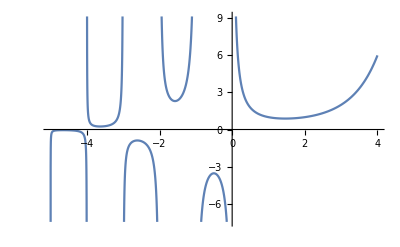

```mathematica
Plot[Gamma[x],{x,-5,4}]
```

```mathematica
Table[{k,Residue[Gamma[z],{z,-k}]},{k,1,7}]//TableForm
```

1 | -1
2 | 1/2
3 | -1/6
4 | 1/24
5 | -1/120
6 | 1/720
7 | -1/5040

```mathematica
g[n_]:=Product[(1+1/k)^n/(1+n/k),{k,1,Infinity}]
```

```mathematica
g[4]
```

24

```mathematica
π^2/6//N
```

1.64493

```mathematica
Integrate[1/x^2,{x,1,Infinity}]
```

1

```mathematica
Sum[1/k^2,{k,1,Infinity}]//N
```

1.64493

## *Table of Arithmetical Functions ( -under construction- )

### Definition

#### Table

```mathematica
TableForm[{
{"Cell["I",ExpressionUUID->"77878252-9a1d-4b58-b066-202a47535308"]","-","Floor[1/n]","-","CM","I","?","1","1"},
{"1","-","1","-","CM","μ","?",DirichletTransform[1,n,s]//TraditionalForm,"1/(1-x)"},
{"N","-","n","-","CM","μN","?",DirichletTransform[n,n,s]//TraditionalForm,"1/(1-px)"},
{"N^a","a⩾0","n^a","σ_a*μ ; J_a*1","CM","μN^a","x^(a + 1)/(a+1)+O(x^a)",DirichletTransform[n^a,n,s]//TraditionalForm,"1/(1-p^ax)"},
{"μ","Sum of primitive\nn-th roots of unity","MoebiusMu[n]","-","M","1","?",DirichletTransform[MoebiusMu[n],n,s]//TraditionalForm,"1-x"},
{"μ_k","Möbius function of order k","nMoebiusMu[k,n]","-","M","?","?","?","?"},
{"ϕ","Euler Totient function","EulerPhi[n]","μ*N","M","μN*1","3/π^2 x^2 + O(x Log[x])",DirichletTransform[EulerPhi[n],n,s]//TraditionalForm,"(1-x)/(1-px)"},
{"J_k","Jordan Totient function","nJordanTotient[k,n]","μ*N^k ; σ_k*μ*μ","M","μN^k*1","?",DirichletTransform[DirichletConvolve[j^k,MoebiusMu[j],j,n],n,s]//TraditionalForm,"(p^k-1)/(1-p^kx)"},
{"τ","-","DivisorSigma[0,n]","1*1","M","μ*μ","x Log[x]+(2γ-1)x+O(√x)",DirichletTransform[DivisorSigma[0,n],n,s]//TraditionalForm,"1/(1-x)^2"},
{"τ^(k)","The number of ways of expressing n\nas a product of k positive factors","nDirichletPower\n[DivisorSigma[0,#]&,k][n]","1^(k + 1)","M","μ^(k + 1)","?","?","?"},
{"σ","-","DivisorSigma[1,n]","N*1 ; σ=ϕ*τ","M","μ*μN","ζ(2)/2 x^2+O(x Log[x])",DirichletTransform[DivisorSigma[1,n],n,s]//TraditionalForm,"1/((1-px)(1-x))"},
{"σ_a","a≥2","DivisorSigma[a,n]","N^a*1 ; σ_1=ϕ*τ","M","μ*μN^a","ζ(a+1)/(a+1)x^(a + 1)+O(x^a)","s-a s","1/((1-p^ax)(1-x))"},
{"GCD_k","-","GCD[k,n]","-","M","μGCD_k","?","?","?"},
{"γ","Core","-","-","M","?","?","?","(1-(1-p)x)/(1-x)"},
{"λ","-","LiouvilleLambda[n]\n(-1)^PrimeOmega[n]","-","M","μ^2 ; |μ|","?",DirichletTransform[LiouvilleLambda[n],n,s]//TraditionalForm,"1/(1+x)"},
{"μ^2","1 if squarefree, 0 otherwise","-","-","M","λ","?","ζ(s)/ζ(2s)","1+x"},
{"λ*1","1 if square, 0 otherwise","-","-","M","μ^2*μ","?","?","?"},
{"μ^2*1","Number of square-free divisors","2^PrimeNu[n]","|μ|*1","M","λ*μ","?",DirichletTransform[DirichletConvolve[1,Abs[MoebiusMu[j]],j,n],n,s]//TraditionalForm,"(1+x)/(1-x)"},
{"a","Number of abelian groups","FiniteAbelianGroupCount[n]","-","M","?","?","?","?"},
{"ϕ_k","Euler Totient function of order k","nEulerPhi[k,n]","Faulhaber_k*μN^k","-","?","?","?","?"},
{"ν","-","PrimeNu[n]","-","A","None","?","?","?"},
{"Ω","-","PrimeOmega[n]","-","CA","None","?","?","?"},
{"Λ","-","MangoldtLambda[n]","-","-","None","?","-ζ'(s)/ζ(s)","?"},
{"L","-","Log[n]","Λ*1","CA","None","?","?","?"},
{"ν*μ","1 if prime, 0 otherwise","-","-","?","None","?","?","?"},
{"?","1 if k-th-powerfree, 0 otherwise","-","-","?","?","?","ζ(s)/ζ(ks)","?"},
{"?","Von Sterneck function","-","-","?","?","?","?","?"},
{"?","Lehmer Divisor function","-","-","?","?","?","?","?"},
{"?","Ramanujan sum","-","-","?","?","?","?","?"},
{"M_k","Lehmer Inverse","-","-","M","?","?","?","?"},
{"S","Number of divisors of n^2","-","1*2^PrimeNu","M","?","?","?","?"}
},TableHeadings->{None,{"ARF","Remark", "Mathematica","Alt. Def.","(C)M/A/-","Inverse","Asymptotic ∑_(n ⩽ x) ", "Dirichlet Series", "Bell Series"}}]
```

ARF | Remark | Mathematica | Alt. Def. | (C)M/A/- | Inverse | Asymptotic ∑_(n ⩽ x)  | Dirichlet Series | Bell Series
Cell["I"] | - | Floor[1/n] | - | CM | I | ? | 1 | 1
1 | - | 1 | - | CM | μ | ? | s | 1/(1-x)
N | - | n | - | CM | μN | ? | s-1 | 1/(1-px)
N^a | a⩾0 | n^a | σ_a*μ ; J_a*1 | CM | μN^a | x^(a + 1)/(a+1)+O(x^a) | s-a | 1/(1-p^ax)
μ | Sum of primitive
n-th roots of unity | MoebiusMu[n] | - | M | 1 | ? | 1/s | 1-x
μ_k | Möbius function of order k | nMoebiusMu[k,n] | - | M | ? | ? | ? | ?
ϕ | Euler Totient function | EulerPhi[n] | μ*N | M | μN*1 | 3/π^2 x^2 + O(x Log[x]) | (s-1)/s | (1-x)/(1-px)
J_k | Jordan Totient function | nJordanTotient[k,n] | μ*N^k ; σ_k*μ*μ | M | μN^k*1 | ? | (s-k)/s | (p^k-1)/(1-p^kx)
τ | - | DivisorSigma[0,n] | 1*1 | M | μ*μ | x Log[x]+(2γ-1)x+O(√x) | s^2 | 1/(1-x)^2
τ^(k) | The number of ways of expressing n
as a product of k positive factors | nDirichletPower
[DivisorSigma[0,#]&,k][n] | 1^(k + 1) | M | μ^(k + 1) | ? | ? | ?
σ | - | DivisorSigma[1,n] | N*1 ; σ=ϕ*τ | M | μ*μN | ζ(2)/2 x^2+O(x Log[x]) | s-1 s | 1/((1-px)(1-x))
σ_a | a≥2 | DivisorSigma[a,n] | N^a*1 ; σ_1=ϕ*τ | M | μ*μN^a | ζ(a+1)/(a+1)x^(a + 1)+O(x^a) | s-a s | 1/((1-p^ax)(1-x))
GCD_k | - | GCD[k,n] | - | M | μGCD_k | ? | ? | ?
γ | Core | - | - | M | ? | ? | ? | (1-(1-p)x)/(1-x)
λ | - | LiouvilleLambda[n]
(-1)^PrimeOmega[n] | - | M | μ^2 ; |μ| | ? | (2 s)/s | 1/(1+x)
μ^2 | 1 if squarefree, 0 otherwise | - | - | M | λ | ? | ζ(s)/ζ(2s) | 1+x
λ*1 | 1 if square, 0 otherwise | - | - | M | μ^2*μ | ? | ? | ?
μ^2*1 | Number of square-free divisors | 2^PrimeNu[n] | |μ|*1 | M | λ*μ | ? | s^2/(2 s) | (1+x)/(1-x)
a | Number of abelian groups | FiniteAbelianGroupCount[n] | - | M | ? | ? | ? | ?
ϕ_k | Euler Totient function of order k | nEulerPhi[k,n] | Faulhaber_k*μN^k | - | ? | ? | ? | ?
ν | - | PrimeNu[n] | - | A | None | ? | ? | ?
Ω | - | PrimeOmega[n] | - | CA | None | ? | ? | ?
Λ | - | MangoldtLambda[n] | - | - | None | ? | -ζ'(s)/ζ(s) | ?
L | - | Log[n] | Λ*1 | CA | None | ? | ? | ?
ν*μ | 1 if prime, 0 otherwise | - | - | ? | None | ? | ? | ?
? | 1 if k-th-powerfree, 0 otherwise | - | - | ? | ? | ? | ζ(s)/ζ(ks) | ?
? | Von Sterneck function | - | - | ? | ? | ? | ? | ?
? | Lehmer Divisor function | - | - | ? | ? | ? | ? | ?
? | Ramanujan sum | - | - | ? | ? | ? | ? | ?
M_k | Lehmer Inverse | - | - | M | ? | ? | ? | ?
S | Number of divisors of n^2 | - | 1*2^PrimeNu | M | ? | ? | ? | ?

#### Example-1

So...: ∏_(d|n) (-1)^(Ω(d))(μ(n/d))^2=I(n)?

```mathematica
Table[{n,DirichletConvolve[Floor[1/k],DirichletConvolve[(-1)^PrimeOmega[j],Abs[MoebiusMu[j]],j,k],k,n]},{n,1,8}]//tf
DirichletTransform[DirichletConvolve[DivisorSigma[0,k],DirichletConvolve[1,Abs[MoebiusMu[j]],j,k],k,n],n,s]
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0

Zeta[s]^4/Zeta[2 s]

```mathematica
Table[{k,2^PrimeNu[k]},{k,1,8}]//tf
```

1 | 1
2 | 2
3 | 2
4 | 2
5 | 2
6 | 4
7 | 2
8 | 2
9 | 2
10 | 4
11 | 2
12 | 4

## Bijection between ℕ and ℚ

### Experiments

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,101,111}]//tf
```

101 | 5/2
102 | -1/51
103 | 1/51
104 | -2/13
105 | 2/13
106 | -1/53
107 | 1/53
108 | -1/18
109 | 1/18
110 | -1/55
111 | 1/55

```mathematica
nQuotientToNatural[5/2]
nQuotientToNatural[-1/53]
nQuotientToNatural[1/55]
```

101

106

111

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,6606600,6606609}]
```

{{6606600,-110/273},{6606601,110/273},{6606602,-1/3303301},{6606603,1/3303301},{6606604,-1/3303302},{6606605,1/3303302},{6606606,-1/3303303},{6606607,1/3303303},{6606608,-1/1651652},{6606609,1/1651652}}

## Prime Distribution

### Prime-counting function π(x)

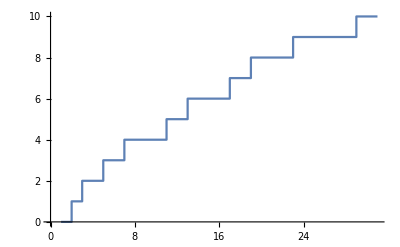

```mathematica
ListStepPlot[Table[{n,PrimePi[n]},{n,30}]]
```

```mathematica
Table[{n,PrimePi[n]},{n,10}]
```

{{1,0},{2,1},{3,2},{4,2},{5,3},{6,3},{7,4},{8,4},{9,4},{10,4}}

```mathematica
primePi2[n_]:=If[n==1,Log[2Pi],If[PrimePowerQ[n],Log[FactorInteger[n][[1,1]]],0]]
Table[primePi2[n],{n,12}]
```

{Log[2 π],Log[2],Log[3],Log[2],Log[5],0,Log[7],Log[2],Log[3],0,Log[11],0}

```mathematica
Solve[{2x +3 y +5 z ==7},{x,y,z},Integers]
```

{{x→ConditionalExpression[C[1], (C[1]|C[2])∈ℤ],y→ConditionalExpression[4+C[1]+5 C[2], (C[1]|C[2])∈ℤ],z→ConditionalExpression[-1-C[1]-3 C[2], (C[1]|C[2])∈ℤ]}}

### Prime-counting function J(x)

```mathematica
heavysideTheta[x_]:=If[x==0,1,HeavisideTheta[x]]
plist[x_]:=Table[y,{y,Select[Range[x],PrimeQ]}]
```

```mathematica
j1[y_]:=Sum[1/n PrimePi[y^(1/n)],{n,1,Ceiling[Log[y]/Log[2]]}]
j2[x_]:=Sum[Sum[1/n heavysideTheta[(x-p^n)],{n,1,Ceiling[Log[x]/Log[2]]}],{p,plist[x]}]
```

```mathematica
j1p[y_]:=Table[1/n PrimePi[y^(1/n)],{n,1,Ceiling[Log[y]/Log[2]]}]
j2p[x_]:=Table[Table[1/n heavysideTheta[(x-p^n)],{n,1,Ceiling[Log[x]/Log[2]]}],{p,plist[x]}]
```

```mathematica
j1p2[y_]:=Table[{1/n,y^(1/n)//N,PrimePi[y^(1/n)]},{n,1,Ceiling[Log[y]/Log[2]]}]
j2p2[x_]:=Table[Table[{1/n,(x-p^n),1/n heavysideTheta[(x-p^n)]},{n,1,Ceiling[Log[x]/Log[2]]}],{p,plist[x]}]
```

```mathematica
j1p[11]//N
j2p[11]//N
```

{5.,1.,0.333333,0.}

{{1.,0.5,0.333333,0.},{1.,0.5,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.}}

## Mellin Transformation